#### Temporal Memory Example - Sine Signal

Peter Overmann, 14 Jul 2022

#### Configuration

```mathematica
Get[  $UserBaseDirectory <> "/TriadicMemory/triadicmemoryC.m"]
Get[  $UserBaseDirectory <> "/TriadicMemory/temporalmemory.m"]
Get[  $UserBaseDirectory <> "/TriadicMemory/encoders.m"]
```

```mathematica
n = 1000; p = 15;
```

```mathematica
TemporalMemory[ T, {n,p}];
```

#### Temporal prediction

```mathematica
predict[x_] := SDR2Real[T[Real2SDR[x, {-1,1}, {n,p}]], {-1,1}, {n,p}]
```

#### Test signal

```mathematica
signal = Table[ Sin[x], {x,0,10Pi, 0.15}];
```

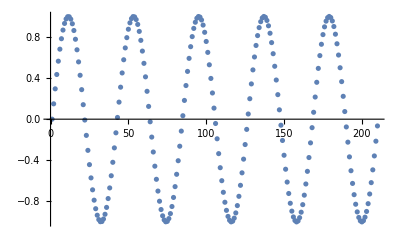

```mathematica
ListPlot[signal]
```

#### Step-by-step predictions during training

Using a temporal associative memory with n = 1000, p = 15.

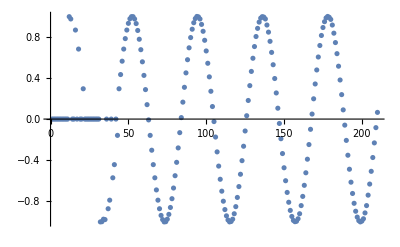

```mathematica
ListPlot[predict /@ signal]
```

#### Auto-playing the sequence

Starting from point 0.5, feeding each prediction back as input for the next step

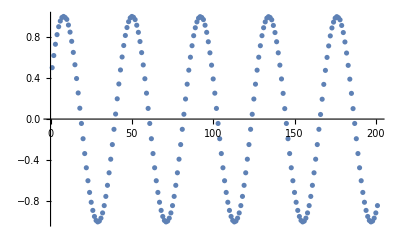

```mathematica
NestList[  predict, 0.5, 200] // ListPlot
```